# Wandering Filter - Time Transition

Similar to the steady state transition, we must also calculate the arc length of the time transition functions for each individual state.

```mathematica
SetDirectory[NotebookDirectory[]];
FCL={20,10,5};
CIAL={80,70,68};
F2L={200,30,20};
F3L={3400,420,60};
FML={100,200,50};
FSL={500,150,300};
MPL={50,8500,20};
O2L={1.0,0.481333,1.22222};

(* Helper function to get easy access to list entry *)
at[list_, index_]:= list[[index]]
nestedAt[list_, index_, index2_]:=at[at[list, index], index2]
```

```mathematica
RegFunction[k_, n_, SP_, C_, x_]:=k/(1+Exp[n*(x-SP)])+C
getk23[list_]:=Module[{fccase,ciacase,f2case,f3case},fccase=RegFunction[0.293708,-0.248768,15.105,0,FC[t]];
ciacase=RegFunction[0.227484,-0.652642,71.4237,0,CIA[t]];
f2case=RegFunction[0.226644,-0.130635,37.073,0,F2[t]];
f3case=RegFunction[0.226655,-0.00362872,674.652,0,F3[t]];
Switch[list,FCL,fccase,CIAL,ciacase,F2L,f2case,F3L,f3case]]
getkO2[list_]:=Module[{fscase},fscase=RegFunction[95.3616,-0.0134783,258.284,0,FS[t]];
Switch[list,FSL,fscase]]
getkCIA[list_]:=Module[{o2case,fmcase,mpcase},o2case=RegFunction[4.661,-8.87757,1.41475,0.418826,O2[t]];
fmcase=RegFunction[5.50768,0.0387998,0.991932,0.41756,FM[t]];
mpcase=RegFunction[3.006,0.0690787,3.09565,0.42,MP[t]];
Switch[list,O2L,o2case,FML,fmcase,MPL,mpcase]]
getkCYT[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[16.6101,0.159447,7.90727,2.62995,F2[t]];
ciacase=RegFunction[1557.4,0.744197,59.1271,2.62967,CIA[t]];
f3case=RegFunction[5.00448,0.00537466,0.991933,2.62995,F3[t]];
fccase=RegFunction[2.15854,1.00162,8.74028,2.62992,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
getkMIT[list_]:=Module[{fscase},fscase=RegFunction[168.632,0.022031,0.991933,0.538779,FS[t]];
Switch[list,FSL,fscase]]
getkMP[list_]:=Module[{o2case,mpcase,fmcase},o2case=RegFunction[4.1828,8.89003,0.130172,0,O2[t]];
mpcase=RegFunction[0.176593,-0.0142367,376.877,0,MP[t]];
fmcase=RegFunction[0.931282,-0.0587368,224.854,0.00105854,FM[t]];
Switch[list,O2L,o2case,MPL,mpcase,FML,fmcase]]
getkVAC[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[2.99975,-0.076787,56.8973,0,F2[t]];
ciacase=RegFunction[3.67913,-0.377767,76.0689,0,CIA[t]];
f3case=RegFunction[3.04175,-0.00213037,1396.83,0,F3[t]];
fccase=RegFunction[2.88787,-0.679725,14.0134,0.160357,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
```

We calculate all the arc lengths for the 146 cases.

```mathematica
cases ={{FCL,FML,FCL,FSL,FCL,FSL,FML},{FCL,FML,FCL,FSL,FCL,FSL,MPL},{FCL,FML,FCL,FSL,F2L,FSL,FML},{FCL,FML,FCL,FSL,F2L,FSL,MPL},{FCL,FML,FCL,FSL,F3L,FSL,FML},{FCL,FML,FCL,FSL,F3L,FSL,MPL},{FCL,FML,CIAL,FSL,FCL,FSL,FML},{FCL,FML,CIAL,FSL,FCL,FSL,MPL},{FCL,FML,CIAL,FSL,F3L,FSL,FML},{FCL,FML,CIAL,FSL,F3L,FSL,MPL},{FCL,FML,F3L,FSL,F3L,FSL,FML},{FCL,FML,F3L,FSL,F3L,FSL,MPL},{FCL,MPL,FCL,FSL,FCL,FSL,FML},{FCL,MPL,FCL,FSL,FCL,FSL,MPL},{FCL,MPL,FCL,FSL,CIAL,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,MPL},{FCL,MPL,FCL,FSL,F3L,FSL,FML},{FCL,MPL,FCL,FSL,F3L,FSL,MPL},{FCL,MPL,CIAL,FSL,FCL,FSL,MPL},{FCL,MPL,CIAL,FSL,F3L,FSL,MPL},{FCL,MPL,F3L,FSL,F3L,FSL,FML},{FCL,MPL,F3L,FSL,F3L,FSL,MPL},{FCL,O2L,FCL,FSL,FCL,FSL,FML},{FCL,O2L,FCL,FSL,FCL,FSL,MPL},{FCL,O2L,FCL,FSL,CIAL,FSL,FML},{FCL,O2L,FCL,FSL,CIAL,FSL,MPL},{FCL,O2L,FCL,FSL,F2L,FSL,FML},{FCL,O2L,FCL,FSL,F2L,FSL,MPL},{FCL,O2L,FCL,FSL,F3L,FSL,FML},{FCL,O2L,FCL,FSL,F3L,FSL,MPL},{FCL,O2L,F3L,FSL,F3L,FSL,FML},{FCL,O2L,F3L,FSL,F3L,FSL,MPL},{CIAL,FML,FCL,FSL,FCL,FSL,FML},{CIAL,FML,FCL,FSL,FCL,FSL,MPL},{CIAL,FML,FCL,FSL,F3L,FSL,FML},{CIAL,FML,FCL,FSL,F3L,FSL,MPL},{CIAL,FML,CIAL,FSL,FCL,FSL,FML},{CIAL,FML,CIAL,FSL,FCL,FSL,MPL},{CIAL,FML,CIAL,FSL,F3L,FSL,FML},{CIAL,FML,CIAL,FSL,F3L,FSL,MPL},{CIAL,FML,F3L,FSL,FCL,FSL,FML},{CIAL,FML,F3L,FSL,FCL,FSL,MPL},{CIAL,FML,F3L,FSL,F3L,FSL,FML},{CIAL,FML,F3L,FSL,F3L,FSL,MPL},{CIAL,MPL,FCL,FSL,FCL,FSL,FML},{CIAL,MPL,FCL,FSL,FCL,FSL,MPL},{CIAL,MPL,FCL,FSL,CIAL,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,MPL},{CIAL,MPL,CIAL,FSL,FCL,FSL,MPL},{CIAL,MPL,CIAL,FSL,F3L,FSL,MPL},{CIAL,MPL,F3L,FSL,FCL,FSL,FML},{CIAL,MPL,F3L,FSL,FCL,FSL,MPL},{CIAL,MPL,F3L,FSL,F3L,FSL,FML},{CIAL,MPL,F3L,FSL,F3L,FSL,MPL},{CIAL,O2L,FCL,FSL,FCL,FSL,FML},{CIAL,O2L,FCL,FSL,FCL,FSL,MPL},{CIAL,O2L,FCL,FSL,CIAL,FSL,FML},{CIAL,O2L,FCL,FSL,CIAL,FSL,MPL},{CIAL,O2L,FCL,FSL,F3L,FSL,FML},{CIAL,O2L,FCL,FSL,F3L,FSL,MPL},{CIAL,O2L,F3L,FSL,FCL,FSL,FML},{CIAL,O2L,F3L,FSL,FCL,FSL,MPL},{CIAL,O2L,F3L,FSL,F3L,FSL,FML},{CIAL,O2L,F3L,FSL,F3L,FSL,MPL},{F2L,FML,FCL,FSL,FCL,FSL,FML},{F2L,FML,FCL,FSL,FCL,FSL,MPL},{F2L,FML,FCL,FSL,F2L,FSL,FML},{F2L,FML,FCL,FSL,F2L,FSL,MPL},{F2L,FML,FCL,FSL,F3L,FSL,FML},{F2L,FML,FCL,FSL,F3L,FSL,MPL},{F2L,FML,CIAL,FSL,FCL,FSL,FML},{F2L,FML,CIAL,FSL,FCL,FSL,MPL},{F2L,FML,CIAL,FSL,F2L,FSL,FML},{F2L,FML,CIAL,FSL,F2L,FSL,MPL},{F2L,FML,CIAL,FSL,F3L,FSL,FML},{F2L,FML,CIAL,FSL,F3L,FSL,MPL},{F2L,FML,F2L,FSL,FCL,FSL,FML},{F2L,FML,F2L,FSL,FCL,FSL,MPL},{F2L,FML,F2L,FSL,F2L,FSL,FML},{F2L,FML,F2L,FSL,F2L,FSL,MPL},{F2L,FML,F2L,FSL,F3L,FSL,FML},{F2L,FML,F2L,FSL,F3L,FSL,MPL},{F2L,FML,F3L,FSL,F2L,FSL,MPL},{F2L,FML,F3L,FSL,F3L,FSL,MPL},{F2L,MPL,FCL,FSL,FCL,FSL,FML},{F2L,MPL,FCL,FSL,FCL,FSL,MPL},{F2L,MPL,FCL,FSL,CIAL,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,MPL},{F2L,MPL,FCL,FSL,F3L,FSL,FML},{F2L,MPL,FCL,FSL,F3L,FSL,MPL},{F2L,MPL,CIAL,FSL,FCL,FSL,MPL},{F2L,MPL,CIAL,FSL,F3L,FSL,MPL},{F2L,MPL,F2L,FSL,FCL,FSL,FML},{F2L,MPL,F2L,FSL,FCL,FSL,MPL},{F2L,MPL,F2L,FSL,CIAL,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,MPL},{F2L,MPL,F2L,FSL,F3L,FSL,FML},{F2L,MPL,F2L,FSL,F3L,FSL,MPL},{F2L,MPL,F3L,FSL,F2L,FSL,MPL},{F2L,MPL,F3L,FSL,F3L,FSL,MPL},{F2L,O2L,FCL,FSL,FCL,FSL,FML},{F2L,O2L,FCL,FSL,FCL,FSL,MPL},{F2L,O2L,FCL,FSL,CIAL,FSL,FML},{F2L,O2L,FCL,FSL,CIAL,FSL,MPL},{F2L,O2L,FCL,FSL,F2L,FSL,FML},{F2L,O2L,FCL,FSL,F2L,FSL,MPL},{F2L,O2L,FCL,FSL,F3L,FSL,FML},{F2L,O2L,FCL,FSL,F3L,FSL,MPL},{F2L,O2L,F2L,FSL,FCL,FSL,FML},{F2L,O2L,F2L,FSL,FCL,FSL,MPL},{F2L,O2L,F2L,FSL,CIAL,FSL,FML},{F2L,O2L,F2L,FSL,CIAL,FSL,MPL},{F2L,O2L,F2L,FSL,F2L,FSL,FML},{F2L,O2L,F2L,FSL,F2L,FSL,MPL},{F2L,O2L,F2L,FSL,F3L,FSL,FML},{F2L,O2L,F2L,FSL,F3L,FSL,MPL},{F2L,O2L,F3L,FSL,F2L,FSL,MPL},{F2L,O2L,F3L,FSL,F3L,FSL,MPL},{F3L,FML,FCL,FSL,FCL,FSL,FML},{F3L,FML,FCL,FSL,FCL,FSL,MPL},{F3L,FML,FCL,FSL,F3L,FSL,FML},{F3L,FML,FCL,FSL,F3L,FSL,MPL},{F3L,FML,CIAL,FSL,FCL,FSL,FML},{F3L,FML,CIAL,FSL,FCL,FSL,MPL},{F3L,FML,CIAL,FSL,F3L,FSL,FML},{F3L,FML,CIAL,FSL,F3L,FSL,MPL},{F3L,FML,F3L,FSL,F3L,FSL,MPL},{F3L,MPL,FCL,FSL,FCL,FSL,FML},{F3L,MPL,FCL,FSL,FCL,FSL,MPL},{F3L,MPL,FCL,FSL,CIAL,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,MPL},{F3L,MPL,CIAL,FSL,FCL,FSL,MPL},{F3L,MPL,CIAL,FSL,F3L,FSL,MPL},{F3L,MPL,F3L,FSL,F3L,FSL,MPL},{F3L,O2L,FCL,FSL,FCL,FSL,FML},{F3L,O2L,FCL,FSL,FCL,FSL,MPL},{F3L,O2L,FCL,FSL,CIAL,FSL,FML},{F3L,O2L,FCL,FSL,CIAL,FSL,MPL},{F3L,O2L,FCL,FSL,F3L,FSL,FML},{F3L,O2L,FCL,FSL,F3L,FSL,MPL},{F3L,O2L,F3L,FSL,F3L,FSL,MPL}};
Length[cases]
```

146

We can modify our steady state generator code to calculate wandering scores.  But we need to calculate the arc length however. Fortunately, Wolfram has a builtin function to take care of this.

```mathematica
getWanderingScoreOfComponent[function_] := Module[{t, simArcLength, minArcLength},
minArcLength = EuclideanDistance[{0,function[0]},{5000, function[5000]}];
simArcLength = ArcLength[function[t], {t, 0, 5000}];
 Abs[(simArcLength - minArcLength)]/minArcLength * 100.0
]
```

```mathematica
getWDWanderingScore[Fe_, regs_]:=
Module[{alpha, IRON, k32, kisu, Kcyt, Kvac, Kcia, Kisu, KresO2,Kmit,OXYGEN, K32NAH, CARBON, kres, kNAH, k23, kcia, kvac, kmp, kmit, kcyt, kO2, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, R32, RNAH, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, ode9, eqns, s, x,y,z,b,c,d,n,g,k,k0,k1,k2,k3,k4,k5, k6, k7, k8, k9, line,stream,KF2,O2SP,fcyt,fvac,fmit, mpwandering, fcwandering, f2wandering, ciawandering, fswandering, f3wandering, o2wandering, fmwandering},

IRON = Fe;

kisu =6.666; 
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
O2SP = 1; 
OXYGEN = 100; 
 CARBON = 100; 
kres =36.363636363636363636364;




k23 = at[regs, 1];
kcia = at[regs, 2];
kvac =at[regs, 3];
kmit =at[regs, 4];
kcyt =at[regs, 5];
kO2 = at[regs, 6];
kmp =at[regs,7];
Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt = 0.8;
fmit = 0.1;
fvac = 0.1; 
ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];
ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];
eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==20, CIA[0]==80, F2[0] == 200, F3[0]==3400, FM[0]==100,MP[0]== 50, FS[0]==500, O2[0]== 1};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, 500000}];
<<NumericalCalculus`;

mpwandering = getWanderingScoreOfComponent[MP /. First@s];
fcwandering =getWanderingScoreOfComponent[FC /. First@s];
f2wandering = getWanderingScoreOfComponent[F2 /. First@s];
ciawandering= getWanderingScoreOfComponent[CIA /. First@s];
fswandering =  getWanderingScoreOfComponent[FS /. First@s];
f3wandering =  getWanderingScoreOfComponent[F3 /. First@s];
o2wandering =  getWanderingScoreOfComponent[O2 /. First@s];
fmwandering = getWanderingScoreOfComponent[FM /. First@s];
	Mean[{mpwandering, fcwandering, f2wandering, ciawandering, fswandering, f3wandering, o2wandering, fmwandering}]



];
```

```mathematica
getWYWanderingScore[expression_, regs_]:=
Module[{alpha, IRON, k32, kisu, Kcyt, Kvac, Kcia, Kisu, KresO2, KresNAH, K32, Kmit,OXYGEN, K32NAH, CARBON, kres, kNAH, k23, kcia, kvac, kmp, kmit, kcyt, kO2, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, R32, RNAH, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, ode9, eqns, s, x,y,z,b,c,d,n,g,k,k0,k1,k2,k3,k4,k5, k6, k7, k8, k9, line,stream,KF2,O2SP, fcyt,fvac,fmit,  mpwandering, fcwandering, f2wandering, ciawandering, fswandering, f3wandering, o2wandering, fmwandering},

IRON = 40;
k32 = 1;
kisu =expression; 
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
K32 = 800;
O2SP = 1; 
OXYGEN = 100; 
 CARBON = 100; 
kres =36.363636363636363636364;


k23 = at[regs, 1];
kcia = at[regs, 2];
kvac =at[regs, 3];
kmit =at[regs, 4];
kcyt =at[regs, 5];
kO2 = at[regs, 6];
kmp = at[regs,7];

Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt=0.8;
fmit=0.1;
fvac=0.1;

ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];
eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==20, CIA[0]==80, F2[0] == 200, F3[0]==3400, FM[0]==100,MP[0]== 50, FS[0]==500, O2[0]== 1};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, 500000}];
<<NumericalCalculus`;

mpwandering = getWanderingScoreOfComponent[MP /. First@s];
fcwandering =getWanderingScoreOfComponent[FC /. First@s];
f2wandering = getWanderingScoreOfComponent[F2 /. First@s];
ciawandering= getWanderingScoreOfComponent[CIA /. First@s];
fswandering =  getWanderingScoreOfComponent[FS /. First@s];
f3wandering =  getWanderingScoreOfComponent[F3 /. First@s];
o2wandering =  getWanderingScoreOfComponent[O2 /. First@s];
fmwandering = getWanderingScoreOfComponent[FM /. First@s];
	Mean[{mpwandering, fcwandering, f2wandering, ciawandering, fswandering, f3wandering, o2wandering, fmwandering}]
];
```

A progress bar has been added since this computation takes a fairly long time to complete.

```mathematica
wanderingscores = {};
indexAt = 0;
ProgressIndicator[Dynamic[indexAt],{0,146}]
For[i=1, i ≤146, i+=1,
regs = {0,0,0,0,0,0,0};
case = at[cases, i];

regs[[1]] = getk23[at[case, 1]];
regs[[2]] = getkCIA[at[case, 2]];
regs[[3]] = getkVAC[at[case, 3]];
regs[[4]] = getkMIT[at[case, 4]];
regs[[5]] = getkCYT[at[case, 5]];
regs[[6]] = getkO2[at[case, 6]];
regs[[7]] = getkMP[at[case,7]];
dscore = getWDWanderingScore[1, regs];
yscore = getWYWanderingScore[6.666/10, regs];
wanderingscore =(dscore + yscore)/2.0;
AppendTo[wanderingscores, wanderingscore];
indexAt = i;
]
wanderingscores
```

{5.93349,5.81987,5.99876,5.88697,5.99215,5.91652,6.59242,8.15979,7.32305,8.60942,6.0928,6.09255,5.91623,6.44846,5.9001,5.96861,6.50333,5.96931,6.52804,7.31677,8.0921,6.0934,6.53223,4.9192,5.40352,4.94552,5.46175,4.96146,5.44561,4.94716,5.45545,5.46684,5.74611,6.13803,6.0458,6.3483,6.20232,6.38358,6.06544,6.92984,6.58393,8.38407,7.96134,8.6071,7.54468,6.1835,6.74272,6.18312,6.33099,7.18201,6.88725,7.63483,8.57846,9.19785,8.70084,9.39019,5.20188,5.68603,5.26332,5.78263,5.33371,5.90264,7.60974,8.02985,7.40219,7.91464,6.14428,6.05526,6.14506,6.05584,6.21876,6.16676,6.36981,6.05031,6.61131,6.08186,6.90136,6.54996,6.01146,6.03129,6.27695,6.12664,6.20805,6.11529,4.98144,4.92821,6.12063,6.65449,6.12276,6.13273,6.66965,6.19026,6.74851,6.87907,7.61686,5.97298,6.57044,6.15087,6.26398,6.7739,6.17837,6.72892,5.66616,5.60612,5.20852,5.6913,5.24861,5.7617,5.2098,5.69275,5.25418,5.75943,5.34637,5.85446,5.50847,5.98445,5.5641,5.98755,5.46425,5.92855,4.8004,4.74446,6.14372,6.05607,6.21944,6.17019,6.36597,6.04823,6.93485,6.71065,4.98826,6.11993,6.6559,6.12216,6.1903,6.75184,6.88194,7.7525,5.66546,5.20804,5.69262,5.249,5.76428,5.25451,5.76311,4.80052}

Let us take a quick look at these wandering scores. The Ordering function lets us sort by position.  We want the upper half of cases (50th percentile and above).

{122,121,146,24,86,26,30,28,85,131,57,140,105,109,107,142,111,144,59,61,113,25,29,31,27,119,32,115,117,104,139,103,58,106,141,110,33,112,108,145,143,60,2,114,4,15,62,13,6,120,1,16,18,96,116,118,5,3,79,80,35,128,74,68,70,124,39,76,12,11,22,84,132}

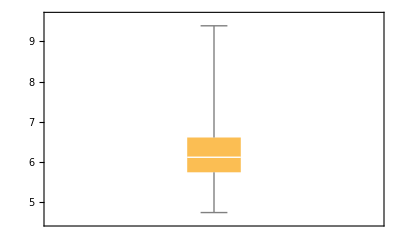

```mathematica
Ordering[wanderingscores, 146/2]
BoxWhiskerChart[wanderingscores]
```

Now we should take the intersection of the top 73 cases between the steady state scores and the time transition wandering scores.

```mathematica
steadyStateValues = {69,67,71,123,125,3,1,5,36,34,87,90,92,132,135,89,16,134,13,18,15,79,96,38,73,127,81,98,83,48,99,101,7,11,42,44,22,75,77,40,129,53,55,49,46,107,109,105,111,26,28,24,30,142,140,144,59,61,57,9,94,51,137,95,52,138,93,136,91,88,133,19,17};
Length[steadyStateValues]
results = Intersection[steadyStateValues, Ordering[wanderingscores, 146/2]]
```

73

{1,3,5,11,13,15,16,18,22,24,26,28,30,57,59,61,79,96,105,107,109,111,132,140,142,144}

```mathematica
Length[results]
```

26